CONFIGURAÇÕES INICIAIS

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[{ListPlot, ListLogPlot, ListLinePlot, ListLogLinearPlot,ListLogLogPlot}, BaseStyle -> {Black, FontFamily -> "Helvetica", 12}, 
  ImageSize -> 600, Joined -> True, PlotStyle -> Thick, Axes -> False, Frame -> True];
SetOptions[{BarChart, DateListPlot}, BaseStyle -> {Black, FontFamily -> "Helvetica", 12}, ImageSize -> 600,Axes -> False, Frame -> True];
```

DADOS EXTRAIDOS DO ARQUIVO BASE

```mathematica
Irdlat = {5.29, 5.41, 5.38, 4.56, 4.76, 4.14, 4.85, 4.77, 4.47, 4.74, 
   4.85, 5.01};
Irdpla = {5.86, 5.67, 5.22, 4.06, 3.83, 3.22, 3.78, 4.06, 4.22, 4.86, 
   5.28, 5.61};
mlatm = Sum[Irdlat[[i]]/Length[Irdlat], {i, 12}];
mplam = Sum[Irdpla[[i]]/Length[Irdpla], {i, 12}];
mdlat = Table[mlatm, {n, 1, 12}];
mdpla = Table[mplam, {n, 1, 12}];
idtpl = DateListPlot[{Irdlat, Irdpla, mdlat, mdpla}, {{2014, 1, 1}, 
   Automatic, "Month"},
  FrameLabel -> {"Month",  
    HoldForm["Average irradiance (kWh/m.b2.day)"]}, 
  LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 14}, 
  PlotLegends -> 
   Placed[LineLegend[{"Latitude angle", "Horizontal plane angle", 
      "Average of latitude", 
      "Average of horizontal plane"}], {.6, .83}], 
  PlotStyle -> {{Black, Thickness[0.0025]}, {Black, Dashing[Large], 
     Thickness[0.0025]}, {Black, DotDashed, Thickness[0.0025]}}, 
  PlotMarkers -> {Automatic, 14}, PlotRange -> All];
```

```mathematica
Export["irradiação.pdf", idtpl];
Export["irradiação.png", idtpl];
```

```mathematica
consum = {886.44, 804.94, 951.08, 944.32, 493.85, 444.45, 485.41, 
   841.64, 893.42, 886.88, 859.3, 886.41};
charge = {383.93, 358.4, 396.75, 383.98, 396.78, 383.98, 396.78, 
   396.78, 383.98, 396.78, 383.98, 396.78};
perdcharge = {7.6787, 7.1679, 7.935, 7.6797, 7.9356, 7.6797, 7.9356, 
   7.9356, 7.6796, 7.9356, 7.6796, 7.9356};
injet = {1095.7, 994.06, 1113.6, 905.06, 1019.9, 845.87, 1053.2, 
   997.69, 921.67, 1022.6, 987.64, 1058.8};
absorv = {1169, 1068.6, 1256.1, 1259.7, 840.44, 786.02, 833.18, 
   1172.2, 1207.2, 1209.2, 1161, 1185.2};
autocons = {102.1, 95.378, 92.529, 69.434, 51.032, 43.245, 49.887, 
   67.012, 70.943, 75.351, 83.117, 98.771};
conex = Table[100, {i, 1, 12}];
```

```mathematica
blc00 = Table[injet[[n]] - absorv[[n]], {n, 1, 12}];
excedplt00 = 
  BarChart[blc00/100, 
   ChartLabels -> {"Jan", "Feb", "Mar", "Apr", "May", "Jun", "Jul", 
     "Aug", "Sep", "Oct", "Nov", "Dec"}, ChartStyle -> {Black}, 
   BarSpacing -> .65, PerformanceGoal -> "Speed", 
   BaseStyle -> {Black, FontFamily -> "Helvetica", 12}, 
   ImageSize -> 600,
   Axes -> False, Frame -> True, 
   FrameLabel -> {"Month",  
     HoldForm["Active energy difference (x10.b2 kWh)"]}, 
   LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 14}];
balanco01 = Show[{
   excedplt00,
   Graphics[{Black, Dashed, Line[{{.55, -1}, {12, -1}}]}],
   Graphics[{Arrowheads[.03], {Black, 
      Arrow[{{8, -3.1}, {6, -1}}, 0.1]}}], 
   Graphics[{Black, 
     Text[Style["Three-phase availability quota", 14], {9, -3.3}]}]}, 
  Axes -> True];
```

```mathematica
Export["balanco01.pdf", balanco01];
Export["balanco01.png", balanco01];
blc01 = Table[
  If[blc00[[n]] > -conex[[n]], conex[[n]], -blc00[[n]]], {n, 1, 12}];
bns00 = Table[
  If[blc00[[n]] > 0, blc00[[n]] + conex[[n]], 0], {n, 1, 12}];
excedplt02 = 
  BarChart[blc01/100, 
   ChartLabels -> {"Jan", "Feb", "Mar", "Apr", "May", "Jun", "Jul", 
     "Aug", "Sep", "Oct", "Nov", "Dec"}, 
   ChartStyle -> {Directive[Black, Opacity[.4]]}, BarSpacing -> .65, 
   PerformanceGoal -> "Speed", 
   BaseStyle -> {Black, FontFamily -> "Helvetica", 12}, 
   ImageSize -> 600, Axes -> False, Frame -> True, 
   FrameLabel -> {"Month",  HoldForm["Active energy (x10.b2 kWh)"]}, 
   LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 14}];
excedplt03 = 
  BarChart[bns00/100, 
   ChartLabels -> {"Jan", "Feb", "Mar", "Apr", "May", "Jun", "Jul", 
     "Aug", "Sep", "Oct", "Nov", "Dec"}, 
   ChartStyle -> {Directive[Black, Opacity[0.1]]}, BarSpacing -> .65, 
   PerformanceGoal -> "Speed", 
   BaseStyle -> {Black, FontFamily -> "Helvetica", 12}, 
   ImageSize -> 600, Axes -> False, Frame -> True, 
   FrameLabel -> {"Month",  HoldForm["Active energy (x10.b2 kWh)"]}, 
   LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 14}];
excedplt05 = 
  BarChart[conex/100, 
   ChartLabels -> {"Jan", "Feb", "Mar", "Apr", "May", "Jun", "Jul", 
     "Aug", "Sep", "Oct", "Nov", "Dec"}, 
   ChartStyle -> {Directive[Black, Opacity[1]]}, BarSpacing -> .65, 
   PerformanceGoal -> "Speed", 
   BaseStyle -> {Black, FontFamily -> "Helvetica", 12}, 
   ImageSize -> 600, Axes -> False, Frame -> True, 
   FrameLabel -> {"Month",  HoldForm["Active energy (x10.b2 kWh)"]}, 
   LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 14}];
balanco02 = Show[{
   excedplt03,
   excedplt02,
   excedplt05,
   Graphics[{Directive[Black, Opacity[0.4]], 
     Rectangle[{8, 3.2}, {8.24, 3.32}]}],
   Graphics[{Directive[Black, Opacity[0.1]], 
     Rectangle[{8, 3.4}, {8.24, 3.52}]}],
   Graphics[{Directive[Black, Opacity[1]], 
     Rectangle[{8, 3.0}, {8.24, 3.12}]}], 
   Graphics[{Black, 
     Text[Style["Availability quota/month", 14], {10.1, 3.05}]}],
   Graphics[{Black, 
     Text[Style["Excess consumption/month", 14], {10.3, 3.25}]}],
   Graphics[{Black, 
     Text[Style["Energy bonus/month", 14], {9.856, 3.45}]}]}, 
  Axes -> True, PlotRange -> All];
```

```mathematica
bns01 =
 Table[
  If[blc00[[n]] < 0,
   If[blc00[[n]] > -conex[[n]], 0, conex[[n]] + blc00[[n]]], 
   bns00[[n]] - conex[[n]]]
  , {n, 1, 12}];

tt = {0, 0, 0, 0, 179.459, 59.85, 
   220.02, -74.51, -185.53, -86.60, -73.36, -26.4};
Table[bns01[[l]] + Sum[bns01[[n - 1]], {n, 2, l}], {l, 2, 12}];

acumul = 
 Join[{0}, Table[tt[[l]] + Sum[tt[[n - 1]], {n, 2, l}], {l, 2, 12}]];

excedplt04 = 
 BarChart[(conex + acumul)/100, 
  ChartLabels -> {"Jan", "Feb", "Mar", "Apr", "May", "Jun", "Jul", 
    "Aug", "Sep", "Oct", "Nov", "Dec"}, 
  ChartStyle -> {Directive[Black, Opacity[.1]]}, BarSpacing -> .65, 
  PerformanceGoal -> "Speed", 
  BaseStyle -> {Black, FontFamily -> "Helvetica", 14}, 
  ImageSize -> 600,
  Axes -> False, Frame -> True,
  FrameLabel -> {"Month",  HoldForm["Accumulated bunus (x10.b2 kWh)"]}, 
  LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 
    14}]; excedplt06 = 
 BarChart[{100, 100, 143.5, 347.87, 100, 100, 100, 100, 100, 100, 100,
     100}/100, 
  ChartLabels -> {"Jan", "Feb", "Mar", "Apr", "May", "Jun", "Jul", 
    "Aug", "Sep", "Oct", "Nov", "Dec"}, 
  ChartStyle -> {Directive[Black, Opacity[1]]}, BarSpacing -> .65, 
  PerformanceGoal -> "Speed", 
  BaseStyle -> {Black, FontFamily -> "Helvetica", 14}, 
  ImageSize -> 600,
  Axes -> False, Frame -> True,
  FrameLabel -> {"Month",  HoldForm["Accumulated bunus (x10.b2 kWh)"]}, 
  LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 14}];
balanco03 = Show[{
   excedplt04,
   excedplt06,
   Graphics[{Directive[Black, Opacity[0.1]], 
     Rectangle[{2, 5.2}, {2.2, 5.4}]}],
   Graphics[{Directive[Black, Opacity[1]], 
     Rectangle[{2, 5.5}, {2.2, 5.7}]}],
   Graphics[{Black, 
     Text[Style["Paid energy/month", 14], {3.69, 5.59}]}],
   Graphics[{Black, 
     Text[Style["Accumulated bouns/month", 14], {4.2, 5.28}]}]}, 
  Axes -> True, PlotRange -> All];

Export["balanco03.pdf", balanco03];
Export["balanco03.png", balanco03];
```

```mathematica
engpl02 = 
 DateListPlot[{absorv, injet, autocons}/1000, {{2014, 1, 1}, 
   Automatic, "Month"},
  FrameLabel -> {"Month",  
    HoldForm["Electrical Energy (10.b3 kWh/month)"]}, 
  LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 14}, 
  PlotLegends -> 
   Placed[LineLegend[{"Absorved of grid", "Injected on grid", 
      "Self-consumption"}], {.7, .45}], 
  PlotStyle -> {{Black, Thickness[0.0025]}, {Black, Dashing[Large], 
     Thickness[0.0025]}, {Black, DotDashed, Thickness[0.0025]}}, 
  PlotMarkers -> {Automatic, 14}];

Export["consumo01.pdf", engpl02];
Export["consumo01.png", engpl02];
```

```mathematica
engpl05 = 
 DateListPlot[{consum + charge + perdcharge, injet + autocons}/
   1000, {{2014, 1, 1}, Automatic, "Month"},
  FrameLabel -> {"Month",  
    HoldForm["Electrical Energy (10.b3 kWh/month)"]}, 
  LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 14}, 
  PlotLegends -> 
   Placed[LineLegend[{"Required energy", 
      "Generated energy"}], {.6, .92}], 
  PlotStyle -> {{Black, Thickness[0.0025]}, {Black, Dashing[Large], 
     Thickness[0.0025]}, {Black, DotDashed, Thickness[0.0025]}}, 
  PlotMarkers -> {Automatic, 14}];
Export["consumo02.pdf", engpl05];
Export["consumo02.png", engpl05];
```

```mathematica
engpl04 = 
 DateListPlot[{autocons/100}, {{2014, 1, 1}, Automatic, "Month"},
  FrameLabel -> {"Month",  
    HoldForm["Electrical Energy (10.b2 kWh/month)"]}, 
  LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 14}, 
  PlotLegends -> Placed[LineLegend[{"Self-consumption"}], {.6, .85}], 
  PlotStyle -> {{Black, Thickness[0.0025]}}];
  Export["consumo03.pdf", engpl04];
Export["consumo03.png", engpl04];
```

```mathematica
engpl06 = 
 DateListPlot[{consum + charge + perdcharge, consum, charge}/
   1000, {{2014, 1, 1}, Automatic, "Month"},
  FrameLabel -> {"Month",  
    HoldForm["Electrical Energy (10.b3 kWh/month)"]}, 
  LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 14}, 
  PlotLegends -> 
   Placed[LineLegend[{"Total Required energy", 
      "Residential consumption", "Vehicular Recharge"}], {.8, .15}], 
  PlotStyle -> {{Black, Thickness[0.0025]}, {Black, Dashing[Large], 
     Thickness[0.0025]}, {Black, DotDashed, Thickness[0.0025]}}, 
  PlotMarkers -> {Automatic, 14}];

Export["consumo04.pdf", engpl06];
Export["consumo04.png", engpl06];
```

VALIDAÇÃO DO CALCULADO PELA METODOLOGIA ANALITICA

```mathematica
Yf = Table[(injet[[n]] + autocons[[n]])/(34*0.260), {n, 1, 12}];
Irdlatmen = {164.39, 149.42, 167.05, 133.17, 144.28, 118.23, 147.15, 
   143.1, 132.62, 148, 145.77, 157.1};
dias = {31, 28, 31, 30, 31, 30, 31, 31, 30, 31, 30, 31};
Yr = N[Table[Irdlatmen[[n]](*Irdlat[[n]]*dias[[n]]*), {n, 1, 12}]];
PR = Table[Yf[[n]]/Yr[[n]], {n, 1, 12}]
Ecalc3 = (34*0.260)*Table[Yr[[n]]*PR[[n]], {n, 1, 12}]


PRc = Table[0.83*365/(12*dias[[n]]), {n, 1, 12}];
PRe = 0.83;
Eideal = (34*.260)*(Irdlat*dias);
Ecalc1 = (34*.260)*(Irdlat*dias)*PRe
Ecalc2 = (34*.260)*Irdlatmen*PRe


engpl07 = 
 DateListPlot[{Ecalc3, (injet + autocons)}/1000, {{2014, 1, 1}, 
   Automatic, "Month"},
  FrameLabel -> {"Month",  
    HoldForm["Electrical Energy (10.b3 kWh/month)"]}, 
  LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 14}, 
  PlotLegends -> 
   Placed[LineLegend[{"Calculated", "PV*Sol"}], {.8, .92}], 
  PlotStyle -> {{Black, Thickness[0.0025]}, {Black, Dashing[Large], 
     Thickness[0.0025]}, {Black, DotDashed, Thickness[0.0025]}}, 
  PlotMarkers -> {Automatic, 14}];

engpl08 = 
 DateListPlot[{(consum + charge + perdcharge), 
    Ecalc1, (injet + autocons)}/1000, {{2014, 1, 1}, Automatic, 
   "Month"},
  FrameLabel -> {"Month",  
    HoldForm["Electrical Energy (10.b3 kWh/month)"]}, 
  LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 14}, 
  PlotLegends -> 
   Placed[LineLegend[{"Required", "Generated (Calculated)", 
      "Generated (PV*Sol)"}], {.8, .15}], 
  PlotStyle -> {{Black, Thickness[0.0025]}, {Black, Dashing[Large], 
     Thickness[0.0025]}, {Black, DotDashed, Thickness[0.0025]}}, 
  PlotMarkers -> {Automatic, 14}];

Export["consumo06.pdf", engpl08];
Export["consumo06.png", engpl08];
```

{0.824246,0.824786,0.816761,0.827791,0.83966,0.850703,0.848003,0.841659,0.846679,0.839207,0.830942,0.833526}

{1197.8,1089.44,1206.13,974.494,1070.93,889.115,1103.09,1064.7,992.613,1097.95,1070.76,1157.57}

{1203.23,1111.44,1223.7,1003.73,1082.68,911.28,1103.15,1084.95,983.919,1078.13,1067.56,1139.54}

{1206.16,1096.32,1225.68,977.095,1058.61,867.477,1079.67,1049.95,973.059,1085.91,1069.54,1152.67}

ANÁLISE AMBIENTAL

{0.258912,0.233856,0.258912,0.25056,0.258912,0.25056,0.258912,0.258912,0.25056,0.258912,0.25056,0.258912}

3.04848

{0.0533663,0.0498176,0.0551483,0.0533732,0.0551524,0.0533732,0.0551524,0.0551524,0.0533732,0.0551524,0.0533732,0.0551524}

{-0.0040032,-0.00289648,0.00694597,0.0396436,-0.0320384,-0.0143302,-0.0375171,0.0149422,0.0298276,0.0154636,0.0125438,0.00384043}

{0,0,0.00694597,0.0396436,0,0,0,0.0149422,0.0298276,0.0154636,0.0125438,0.00384043}

{0.166494,0.151432,0.167652,0.135455,0.14886,0.123587,0.153329,0.147994,0.137973,0.152615,0.148835,0.160902}

{0.37204,0.33547,0.36447,0.292998,0.352619,0.320774,0.357089,0.336811,0.305332,0.340911,0.333478,0.360822}

4.07281

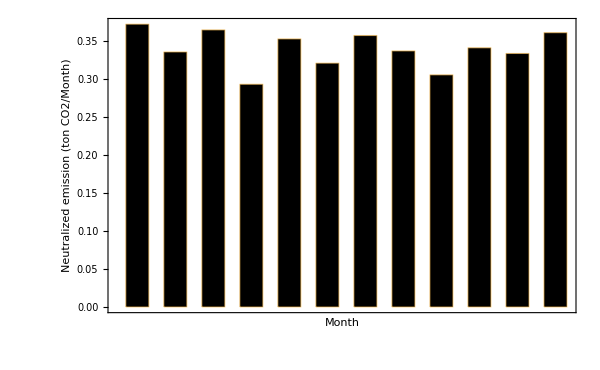

111.099

666.46

```mathematica
fc = 96/10^6;
n = 1;
l = 87;
d = dias;
G1 = N[fc*n*l*d]

Sum[G1[[n]], {n, 1, 12}]

fs = 0.139/1000;
G2 = (charge)*fs

bal = (absorv - (injet + autocons)) fs
G3 = Table[If[bal[[n]] > 0, bal[[n]], 0], {n, 1, 12}]

G4 = (injet + autocons) fs

VECo2 = G1 - G2;
EleCo2 = G4 - G3;
MenCO2 = VECo2 + EleCo2
TotCO2 = Sum[MenCO2[[n]], {n, 1, 12}]

neutral00 = 
 BarChart[MenCO2, 
  ChartLabels -> {"Jan", "Feb", "Mar", "Apr", "May", "Jun", "Jul", 
    "Aug", "Sep", "Oct", "Nov", "Dec"}, ChartStyle -> {Black}, 
  BarSpacing -> .65, PerformanceGoal -> "Speed", 
  BaseStyle -> {Black, FontFamily -> "Helvetica", 12}, 
  ImageSize -> 600,
  Axes -> False, Frame -> True, 
  FrameLabel -> {"Month",  
    HoldForm["Neutralized emission (ton CO2/Month)"]}, 
  LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 14}]

Export["amb01.pdf", neutral00];
Export["amb01.png", neutral00];

fcp = 1.2;
Ima = 2;
Tc = 0.5;
fcc = 44/12;
t = 20;
ffa = 1667;
fix = (Ima  Tc  fcc  t )/ffa;
Ntr = (TotCO2 fcp)/fix
A = Ntr/ffa*10000

Reduct = Table[TotCO2, {n, 1, 20}];
Three = Table[(n/20)* Reduct[[n]], {n, 1, 20}];
thr01 = BarChart[Reduct, 
  ChartLabels -> {"1", "2", "3", "4", "5", "6", "7", "8", "9", "10", 
    "11", "12", "13", "14", "15", "16", "17", "18", "19", "20"}, 
  ChartStyle -> {Directive[Black, Opacity[.1]]}, BarSpacing -> .65, 
  PerformanceGoal -> "Speed", 
  BaseStyle -> {Black, FontFamily -> "Helvetica", 14}, 
  ImageSize -> 600,
  Axes -> False, Frame -> True,
  FrameLabel -> {"Year",  
    HoldForm["Neutralized emission (ton CO2/year)"]}, 
  LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 14}];
thr02 = BarChart[Three, 
  ChartLabels -> {"1", "2", "3", "4", "5", "6", "7", "8", "9", "10", 
    "11", "12", "13", "14", "15", "16", "17", "18", "19", "20"}, 
  ChartStyle -> {Directive[Black, Opacity[1]]}, BarSpacing -> .65, 
  PerformanceGoal -> "Speed", 
  BaseStyle -> {Black, FontFamily -> "Helvetica", 14}, 
  ImageSize -> 600,
  Axes -> False, Frame -> True,
  FrameLabel -> {"Year",  
    HoldForm["Neutralized emission (ton CO2/year)"]}, 
  LabelStyle -> {Directive[Black], FontFamily -> "Helvetica", 14}];

balanco03 = Show[{
   thr01,
   thr02}, Axes -> True, PlotRange -> All];

Export["amb02.pdf", balanco03];
Export["amb02.png", balanco03];
```